# SUSYHelper Guide

## Installation

First install the SUSYHelper.wl file from https://github.com/Gwyerger/SUSYHelper .

Next, run the cell below and follow either path to paste the file. Make sure neither path has an old installation:

```mathematica
FileNameJoin[{$BaseDirectory,"Applications"}]
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

C:\ProgramData\Mathematica\Applications

C:\Users\gabey\AppData\Roaming\Mathematica\Applications

All done. Now be sure that the package runs by getting it and running this notebook:

```mathematica
<<SUSYHelper`
```

## Function Usage

```mathematica
σ[1]
```

{{0,1},{1,0}}

```mathematica
S4[1]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
S8[1]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
PopFirst[{1,0},0]
```

{1}

```mathematica
PopN[{1,1,0}, 0, 2]
```

{1,1}

```mathematica
BitXorList[{{0,1},{1,0},{1,1}}]
```

{{0,0}}

```mathematica
BitXorMapToList[{{0,1},{1,0},{1,1}}, {1,0}]
```

{{1,1},{0,0},{0,1}}

```mathematica
{Ls,Rs} = LRMatricesSP[8];
PauliSearchList[LMatricesSM4D[],"LSM4d"]
PauliSearchList[LMatricesSM10D[], "LSM10d"]
PauliSearchList[LMatricesSM4DValise[],"LSM4dV"]
PauliSearchList[LMatricesVT4DValise[], "LVT4dV"]
```

unsigned

unsigned

unsigned

«13 more identical outputs»

LSM4d1 = B170(1 4 5 8 9 12 14 16 13)
LSM4d2 = B1(2 3 6 7 10 11 13 15 14)
LSM4d3 = B168(3 2 7 6 11 10 16 14 15)
LSM4d4 = B3(4 1 8 5 12 9 15 13 16)
LSM4d5 = B397(5 8 1 4 13 16 10 12 9)
LSM4d6 = B294(6 7 2 3 14 15 9 11 10)
LSM4d7 = B399(7 6 3 2 15 14 12 10 11)
LSM4d8 = B292(8 5 4 1 16 13 11 9 12)
LSM4d9 = B61(9 12 13 16 1 4 6 8 5)
LSM4d10 = B150(10 11 14 15 2 3 5 7 6)
LSM4d11 = B63(11 10 15 14 3 2 8 6 7)
LSM4d12 = B148(12 9 16 13 4 1 7 5 8)
LSM4d13 = B229(13 16 9 12 5 8 2 4 1)
LSM4d14 = B78(14 15 10 11 6 7 1 3 2)
LSM4d15 = B231(15 14 11 10 7 6 4 2 3)
LSM4d16 = B76(16 13 12 9 8 5 3 1 4)

unsigned

unsigned

unsigned

«13 more identical outputs»

LSM10d1 = B168(1 3 4 2 6 5 7 8 16)
LSM10d2 = B484(2 4 3 1 5 6 8 7 15)
LSM10d3 = B412(3 1 2 4 8 7 5 6 14)
LSM10d4 = B208(4 2 1 3 7 8 6 5 13)
LSM10d5 = B376(5 7 8 6 2 1 3 4 12)
LSM10d6 = B52(6 8 7 5 1 2 4 3 11)
LSM10d7 = B76(7 5 6 8 4 3 1 2 10)
LSM10d8 = B256(8 6 5 7 3 4 2 1 9)
LSM10d9 = B340(9 11 12 10 14 13 15 16 8)
LSM10d10 = B24(10 12 11 9 13 14 16 15 7)
LSM10d11 = B96(11 9 10 12 16 15 13 14 6)
LSM10d12 = B300(12 10 9 11 15 16 14 13 5)
LSM10d13 = B132(13 15 16 14 10 9 11 12 4)
LSM10d14 = B456(14 16 15 13 9 10 12 11 3)
LSM10d15 = B432(15 13 14 16 12 11 9 10 2)
LSM10d16 = B252(16 14 13 15 11 12 10 9 1)

unsigned

unsigned

unsigned

«13 more identical outputs»

LSM4dV1 = (0001)(1 4 2 3 5 8 6 7 9 12 10 11 14 16 13 15)
LSM4dV2 = (0010)(2 3 1 4 6 7 5 8 10 11 9 12 13 15 14 16)
LSM4dV3 = B26208(3 2 4 1 7 6 8 5 11 10 12 9 16 14 15 13)
LSM4dV4 = B6(4 1 3 2 8 5 7 6 12 9 11 10 15 13 16 14)
LSM4dV5 = B61515(5 8 6 7 1 4 2 3 13 16 14 15 10 12 9 11)
LSM4dV6 = B38445(6 7 5 8 2 3 1 4 14 15 13 16 9 11 10 12)
LSM4dV7 = B50046(7 6 8 5 3 2 4 1 15 14 16 13 12 10 11 9)
LSM4dV8 = B42264(8 5 7 6 4 1 3 2 16 13 15 14 11 9 12 10)
LSM4dV9 = B1275(9 12 10 11 13 16 14 15 1 4 2 3 6 8 5 7)
LSM4dV10 = B25245(10 11 9 12 14 15 13 16 2 3 1 4 5 7 6 8)
LSM4dV11 = B14286(11 10 12 9 15 14 16 13 3 2 4 1 8 6 7 5)
LSM4dV12 = B20904(12 9 11 10 16 13 15 14 4 1 3 2 7 5 8 6)
LSM4dV13 = B20235(13 16 14 15 9 12 10 11 5 8 6 7 2 4 1 3)
LSM4dV14 = B10605(14 15 13 16 10 11 9 12 6 7 5 8 1 3 2 4)
LSM4dV15 = B31806(15 14 16 13 11 10 12 9 7 6 8 5 4 2 3 1)
LSM4dV16 = B6744(16 13 15 14 12 9 11 10 8 5 7 6 3 1 4 2)

unsigned

unsigned

unsigned

«13 more identical outputs»

LVT4dV1 = B21854(1 4 2 3 6 8 5 7 9 12 10 11 15 16 14 13)
LVT4dV2 = B13108(2 3 1 4 5 7 6 8 10 11 9 12 16 15 13 14)
LVT4dV3 = B24674(3 2 4 1 8 6 7 5 11 10 12 9 13 14 16 15)
LVT4dV4 = B1544(4 1 3 2 7 5 8 6 12 9 11 10 14 13 15 16)
LVT4dV5 = B19408(5 8 6 7 2 4 1 3 13 16 14 15 11 12 10 9)
LVT4dV6 = B11706(6 7 5 8 1 3 2 4 14 15 13 16 12 11 9 10)
LVT4dV7 = B32492(7 6 8 5 4 2 3 1 15 14 16 13 9 10 12 11)
LVT4dV8 = B6278(8 5 7 6 3 1 4 2 16 13 15 14 10 9 11 12)
LVT4dV9 = B46511(9 12 10 11 14 16 13 15 1 4 2 3 7 8 6 5)
LVT4dV10 = B54213(10 11 9 12 13 15 14 16 2 3 1 4 8 7 5 6)
LVT4dV11 = B32915(11 10 12 9 16 14 15 13 3 2 4 1 5 6 8 7)
LVT4dV12 = B59129(12 9 11 10 15 13 16 14 4 1 3 2 6 5 7 8)
LVT4dV13 = B21726(13 16 14 15 10 12 9 11 5 8 6 7 3 4 2 1)
LVT4dV14 = B12980(14 15 13 16 9 11 10 12 6 7 5 8 4 3 1 2)
LVT4dV15 = B25058(15 14 16 13 12 10 11 9 7 6 8 5 1 2 4 3)
LVT4dV16 = B1928(16 13 15 14 11 9 12 10 8 5 7 6 2 1 3 4)

```mathematica
PauliSearchList[Γs[Ls, Rs], "Γ"]
```

Γ1 = (1011)(1001)
Γ2 = (1110)(1010)
Γ3 = (1001)(1011)
Γ4 = (1010)(1110)
Γ5 = (1100)(1101)
Γ6 = (1101)(1100)
Γ7 = B38505(1111)
Γ8 = (1000)

```mathematica
GRdN[Ls,Rs]
```

True

```mathematica
GRdNΓ[Γs[Ls, Rs]]
```

True

```mathematica
MatrixToOneLine[Ls[[1]]]
```

{2,-1,-4,3,6,-5,-8,7}

```mathematica
OneLineToMatrix[{2,-1,-4,3,6,-5,-8,7}]==Ls[[1]]
```

True

```mathematica
PauliSearch[BinaryToMatrix[{1,1,1,1,1,1}],"M"]
```

M = (111111)

```mathematica
Z2Group[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
S2Group[2]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

```mathematica
GLGroup32[];
%[[5]]
```

{{0,0,1},{0,1,1},{1,0,0}}

```mathematica
ReWeight[{MatrixToOneLine[Ls[[1]]], MatrixToOneLine[Ls[[4]]]}]
```

{{2,-1,-4,3,6,-5,-8,7},{7,8,-5,-6,3,4,-1,-2}}

```mathematica
MatricesToTeX[Ls[[;;4]],4 , "L"];
```

L_{1} &= \left(
\begin{array}{cccccccc}
 0 & 1 & 0 & 0 & 0 & 0 & 0 & 0 \\
 -1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & -1 & 0 & 0 & 0 & 0 \\
 0 & 0 & 1 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 1 & 0 & 0 \\
 0 & 0 & 0 & 0 & -1 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & -1 \\
 0 & 0 & 0 & 0 & 0 & 0 & 1 & 0 \\
\end{array}
\right)&L_{2} &= \left(
\begin{array}{cccccccc}
 0 & 0 & 1 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 1 & 0 & 0 & 0 & 0 \\
 -1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & -1 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & -1 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & -1 \\
 0 & 0 & 0 & 0 & 1 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 1 & 0 & 0 \\
\end{array}
\right)&L_{3} &= \left(
\begin{array}{cccccccc}
 0 & 0 & 0 & 1 & 0 & 0 & 0 & 0 \\
 0 & 0 & -1 & 0 & 0 & 0 & 0 & 0 \\
 0 & 1 & 0 & 0 & 0 & 0 & 0 & 0 \\
 -1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 1 \\
 0 & 0 & 0 & 0 & 0 & 0 & -1 & 0 \\
 0 & 0 & 0 & 0 & 0 & 1 & 0 & 0 \\
 0 & 0 & 0 & 0 & -1 & 0 & 0 & 0 \\
\end{array}
\right)&L_{4} &= \left(
\begin{array}{cccccccc}
 0 & 0 & 0 & 0 & 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 1 \\
 0 & 0 & 0 & 0 & -1 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & -1 & 0 & 0 \\
 0 & 0 & 1 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 1 & 0 & 0 & 0 & 0 \\
 -1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & -1 & 0 & 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)&\\

```mathematica
DelimitWith["1010101",","]
```

1,0,1,0,1,0,1

```mathematica
PauliSearchListToBinary[Ls]
```

{{0,0,1},{0,1,0},{0,1,1},{1,1,0},{1,0,1},{1,0,0},{1,1,1},{0,0,0}}

```mathematica
B2NProdSearch[FindBs[Ls][[1]], "B"]
```

B = (011)

```mathematica
S2NProdSearch[FindHRs[Ls][[1,1]], "H"]
```

H = (000)

```mathematica
AddOneInBinary[{1,1,1,1,1}]
```

{0,0,0,0,0}

```mathematica
BracketRep[Ls[[1]],"L"]
```

unsigned

L = (2 1 4 3 6 5 8 7)

```mathematica
BooleanRep[FindBs[Ls][[1]], "B"]
```

B = B102

```mathematica
PauliSearchList[WeightOrder[Ls], "L"]
```

L1 = (000)
L2 = (011)(001)
L3 = (110)(010)
L4 = (001)(011)
L5 = (101)(100)
L6 = (100)(101)
L7 = (010)(110)
L8 = B150(111)

```mathematica
WeightTotal[Abs[Ls]]
```

399999996

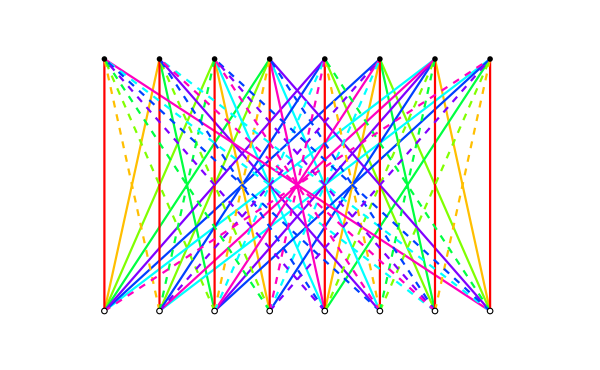

```mathematica
GraphVAdinkra[Ls, Rs]
```

```mathematica
GraphBigVAdinkra[Ls, Rs]
```

-Graphics-

```mathematica
PlotTesseractAdinkra[]
```

-Graphics3D-

```mathematica
PlotProjectedTesseractAdinkra[]
```

-Graphics3D-

```mathematica
{Adjacenecy, AdjacencyM, AdjEigenVals, DistanceM, DistEigenVals, 
     LMatrices} = DecodeNCube[{{1,1,1,1}}]
```

Partitioned Nodes: {8,2,4}

Missed Nodes: {0}

{{{{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}},{{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0}},{{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}},{{0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0},{1,0,0,1,0,1,1,0},{0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0},{0,1,1,0,1,0,0,1},{0,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,0}},{-4,4,0,0,0,0,0,0},{{0,1,1,2,1,2,2,1},{1,0,2,1,2,1,1,2},{1,2,0,1,2,1,1,2},{2,1,1,0,1,2,2,1},{1,2,2,1,0,1,1,2},{2,1,1,2,1,0,2,1},{2,1,1,2,1,2,0,1},{1,2,2,1,2,1,1,0}},{10,-2,-2,-2,-2,-2,-2,2},{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}}

```mathematica
GenerateCode[{{1,1,0,0},{1,0,1,0},{0,0,0,1}}]
```

{{0,0,0,0},{1,1,0,0},{1,0,1,0},{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,0,1,1},{0,1,1,1}}

Connected Graphs: {56,16,16}
Adjacency Spectra: {{-4,4,-2,-2,-2,-2,2,2,2,2,0,0,0,0,0,0}}
Distance Spectra: {{32,-8,-8,-8,-8,0,0,0,0,0,0,0,0,0,0,0}}
Disconnected Graphs: {14,16,16}
Adjacency Spectra: {{-4,-4,4,4,0,0,0,0,0,0,0,0,0,0,0,0}}

{{1},{{-4,4,-2,-2,-2,-2,2,2,2,2,0,0,0,0,0,0}},{{1}},{{{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},4,{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0}},12,{1}},{{-4,-4,4,4,0,0,0,0,0,0,0,0,0,0,0,0}}}
 |  |  |  |

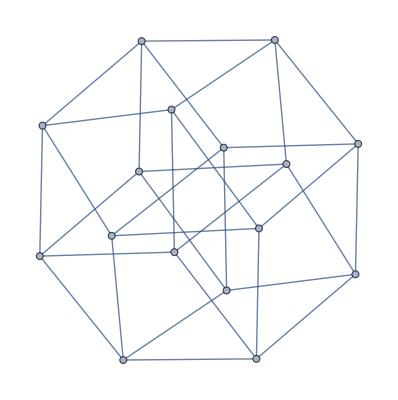

```mathematica
AllSubGraphs[FindHRs[Ls][[1]], 4]
AdjacencyGraph[%[[1,1]]]
```

```mathematica
AllSubAlgebras[Γs[Ls,Rs], 4]
```

n=4-color decomposition: Valid Supermultiplets: {70,4,16,16}
 Fully Connected Supermultiplets: {56,4,16,16}

{{{1},68,{1}},{}}
 |  |  |  |

```mathematica
PauliSearch[OneLineToMatrix[Involutions[8][[1]]],"p"]
```

p = (001)